#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
saveTask = CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

/home/juanathan/Documents/4.- UNAM-PCF-PhD/12-Protocolo/phD-protocolo/1-Calculos

ScheduledTaskObject[…]

```mathematica
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_ThinFilm.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

```mathematica
nDrude[lda_] := Sqrt@DrudeEps[lda,hcPlanckSpeed/10,hcPlanckSpeed/0.02]
```

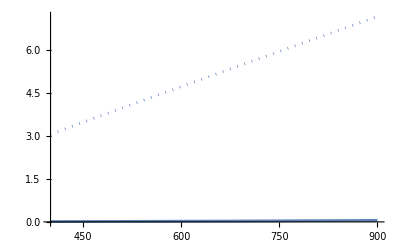

```mathematica
ReImPlot[nDrude[x],{x,400,900}]
```

#### Plots format

```mathematica
PlotGrid = ResourceFunction["PlotGrid"];

ColorMapSuitePath = "~/Documents/Wolfram/ScientificColourMaps8";
ColorMapSuite[name_String] := ColorMapSuite[name, -1]
ColorMapSuite[name_String, el_] := With[{list = Transpose@{Subdivide[0, 1, 255], RGBColor @@@ First @ Import[ColorMapSuitePath <> "/" <> name <> "/" <> name <> ".mat"]}},
                                Blend[list, {##}[[el]]] &]
```

```mathematica
colors = (("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors = ColorMapSuite["lajolla"]/@ Range[0,1,1/13.];
```

```mathematica
fs = 28;
fsI = 24;

texStyle := {FontFamily -> "Latin Modern Roman", FontSize -> fs, Black}
texStyleI := {FontFamily -> "Latin Modern Roman", FontSize -> fsI, Black}
```

```mathematica
graphsOpts1:={Mesh->None, BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1/2.5,
                ImageSize->600,
                PlotStyle->Table[Directive[Thickness[.0075],colors[[i]]],{i,Length[colors]}]}
graphsOpts2:={Mesh->None, BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1/2.5,
                ImageSize->600,
                PlotStyle->Table[Directive[Dashed,Thickness[.0075],colors[[i]]],{i,Length[colors]}]}
                
graphsOpts:= {graphsOpts1,graphsOpts2}
```

```mathematica
graphsOptsD:={BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1,
                ImageSize->300,
                ColorFunction->ColorMapSuite["romaO"]}
graphsOptsPhase := {Mesh->None, BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1,
                ImageSize->300}
```

```mathematica
graphsOptsS1:={Mesh->None, BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1/1.5,
                ImageSize->330,
                PlotStyle->Table[Directive[Thickness[.0075],colors[[i]]],{i,Length[colors]}]}
graphsOptsS2:={Mesh->None, BaseStyle->texStyle, Frame->True,Axes->False,
                FrameStyle->Directive[Thickness[.005],Black],
                AspectRatio->1/1.5,
                ImageSize->330,
                PlotStyle->Table[Directive[Dashed,Thickness[.0075],colors[[i]]],{i,Length[colors]}]}
                
graphsOptsS:= {graphsOptsS1,graphsOptsS2}
```

## SPP - Reflectance

```mathematica
dfilm = 50.;
nNP = JohnsonChristyAuRefSize[#1,#2]& ;

ang = 72*Pi/180.;
nMat = 1.33 + Range[.0,.03,.0025]
```

{1.33,1.3325,1.335,1.3375,1.34,1.3425,1.345,1.3475,1.35,1.3525,1.355,1.3575,1.36}

### SPP Reflectivity

```mathematica
data = ConstantArray[0,{1,2,Length[nMat],Length[lda]}];

i = 1;
lda = Range[450,850,1.];
Table[
  indicesSPP = Transpose[Table[{nm,nNP[i,500],1.5},{i,lda}]];
   
  data[[1,;;,i]] = norm2@ Map[#[ang,Reverse @ indicesSPP,lda, dfilm]&, {Landau3MediaReflectionS,Landau3MediaReflectionP}];
  i++, {nm,nMat}];
```

```mathematica
plots = {0,0};
plots[[1]] = Map[ListLinePlot[#1, Evaluate[graphsOpts[[2]]],DataRange->lda[[{1,-1}]]]&, data[[;;,1]]];
plots[[2]] = Map[ListLinePlot[#1, Evaluate[graphsOpts[[1]]],DataRange->lda[[{1,-1}]]]&, data[[;;,2]]];
plots = Transpose[plots];
```

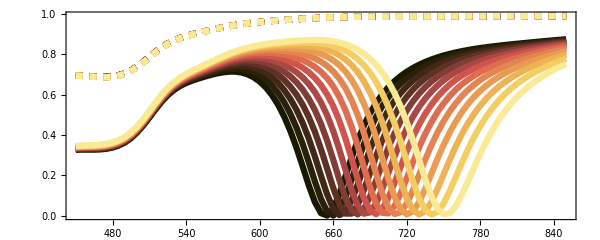

1-Intro-SPP.svg

```mathematica
plot = Show[plots[[1]],DataRange->{450,850},PlotRange->All]
Export["1-Intro-SPP.svg",plot]
```

### Refractive index lable

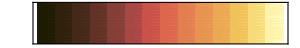

1-Intro-nMscale.svg

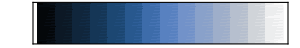

6-Sens-nMscale.svg

```mathematica
plot = DensityPlot[x,{x,0,1},{y,0,1},ColorFunction->ColorMapSuite["lajolla"],
              FrameStyle->Black, BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->fsI,Black},
              PlotRangePadding->None,
              AspectRatio->1/15,
              ImageSize->300,
              FrameTicks-> None]

Export["1-Intro-nMscale.svg",plot]  

plot = DensityPlot[x,{x,0,1},{y,0,1},ColorFunction->ColorMapSuite["oslo"],
              FrameStyle->Black, BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->fsI,Black},
              PlotRangePadding->None,
              AspectRatio->1/15,
              ImageSize->300,
              FrameTicks-> None]

Export["6-Sens-nMscale.svg",plot]
```

## Metasurfaces - Reflectance

```mathematica
aRad = {30.,15.};
cfrac = 0.12; 
rho = (2/3)*((4/3)*π*aRad[[2]]^3)*0.275;
nNP = JohnsonChristyAuRefSize[#1,#2]& ;

ang = 72*Pi/180.;
nMat = 1.33 + Range[.0,.03,.0025]
```

{1.33,1.3325,1.335,1.3375,1.34,1.3425,1.345,1.3475,1.35,1.3525,1.355,1.3575,1.36}

```mathematica
.
```

### VisibleSpectra

```mathematica
data = ConstantArray[0,{2,2,Length[nMat],Length[lda]}];

i = 1;
lda = Range[450,700,5.];
Table[
  indicesCSM = Transpose[Table[{nm,nNP[i,aRad[[1]]],1.5},{i,lda}]];
  epsilon = Transpose[Table[{nm,nNP[i,aRad[[2]]],1.5}^2,{i,lda}]];
  
  data[[1,;;,i]] = norm2 @ CSM3MediaReflectionInt[ang, indicesCSM, lda, aRad[[1]], cfrac];
  data[[2,;;,i]] = norm2@ Map[#[ang,epsilon,lda,aRad[[2]],rho]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
  i++ , {nm,nMat}];
```

```mathematica
plots = {0,0};
plots[[1]] = Map[ListLinePlot[#1, Evaluate[graphsOpts[[2]]],DataRange->{450,700}]&, data[[;;,1]]];
plots[[2]] = Map[ListLinePlot[#1, Evaluate[graphsOpts[[1]]],DataRange->{450,700}]&, data[[;;,2]]];
plots = Transpose[plots];
```

```mathematica
plot = PlotGrid[{#}&/@ Map[Show[#,PlotRange->{{Automatic,700},{Automatic,1.01}}]&,plots] ,Spacings->Scaled[0.02],"ShowFrameLabels"->Automatic,ImageSize->600]
Export["2-ReflNSs.svg",plot]
```

-Graphics-

2-ReflNSs.svg

### Zoom

```mathematica
data = ConstantArray[0,{2,2,Length[nMat],Length[lda]}];

i = 1;
lda = Range[500,600,1];
Table[
  indicesCSM = Transpose[Table[{nm,nNP[i,aRad[[1]]],1.5},{i,lda}]];
  epsilon = Transpose[Table[{nm,nNP[i,aRad[[2]]],1.5}^2,{i,lda}]];
  
  data[[1,;;,i]] = norm2 @ CSM3MediaReflectionInt[ang, indicesCSM, lda, aRad[[1]], cfrac];
  data[[2,;;,i]] = norm2@ Map[#[ang,epsilon,lda,aRad[[2]],rho]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
  i++ , {nm,nMat}];
```

```mathematica
plots = {0,0};
plots[[1]] = Map[ListLinePlot[#1, AspectRatio->1,ImageSize->260,Evaluate[graphsOpts[[2]]],DataRange->lda[[{1,-1}]]]&, data[[;;,1]]];
plots[[2]] = Map[ListLinePlot[#1,AspectRatio->1,ImageSize->260,Evaluate[graphsOpts[[1]]],DataRange->lda[[{1,-1}]]]&, data[[;;,2]]];
plots = Transpose[plots];
```

```mathematica
plot = PlotGrid[{#}&/@ Map[Show[#,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}]&,plots] ,Spacings->Scaled[0.02],"ShowFrameLabels"->Automatic,ImageSize->350]
Export["2-ReflNSs-Zoom.svg",plot]
```

-Graphics-

2-ReflNSs-Zoom.svg

## Metasurfaces - Topological Darkness

```mathematica
aRad = {30.,17.5};
cfrac = 0.12; rho = 0.275/(π*aRad[[2]]^2);
nNP = JohnsonChristyAuRefSize[#1,#2]& ;

nMat = 1.33 ;
```

```mathematica
lda = Range[500.,610,1.];
ang = Range[60.,85.,.25];

indicesCSM = Transpose[Table[{nMat,nNP[i,aRad[[1]]],1.5},{i,lda}]];
epsilon = Transpose[Table[{nMat,nNP[i,aRad[[2]]],1.5}^2,{i,lda}]];

data = {0,0};
data[[1]] = CSM3MediaElipsometryInt[ang*Pi/180, indicesCSM, lda, aRad[[1]], cfrac][[2]];
data[[2]] = ThinFimlElipsometryInt[ang*Pi/180., epsilon, lda, aRad[[2]], rho][[2]];
```

### Color Map

```mathematica
plots = {0,0};
plots[[1]] = ListDensityPlot[Mod[#,2π,-2π]+π,PlotRange->Full,Evaluate[graphsOptsD],DataRange->{lda[[{1,-1}]],ang[[{1,-1}]]},Mesh->None] &@ data[[1]];
plots[[2]] = ListDensityPlot[Mod[#+.19,2π,-2π]+π,PlotRange->Full,Evaluate[graphsOptsD],DataRange->{lda[[{1,-1}]],ang[[{1,-1}]]},Mesh->None] &@ data[[2]];
```

```mathematica
plot = PlotGrid[{plots},Spacings->Scaled[0.02],"ShowFrameLabels"->Automatic,ImageSize->600]
Export["3-TDarkness-CMap.svg",plot]
```

-Graphics-

3-TDarkness-CMap.svg

### Cuts

```mathematica
ang[[49]]
cuts = {0,0};
cuts[[1]] = (Mod[#,2π,-2π]+π) &[data[[1,49]]];
cuts[[2]] = (Mod[#+.19,2π,-2π]+π) &[data[[2,49]]];
```

72.

```mathematica
ticks = Table[{Pi*i,MaTeX[Pi*i,FontSize->fs],{0.01,0}},{i,-5,5,1/2}];
ticks = Join[ticks,Table[{Pi*i,None ,{0.001,0}},{i,-5,5,1/(2*5)}]];
```

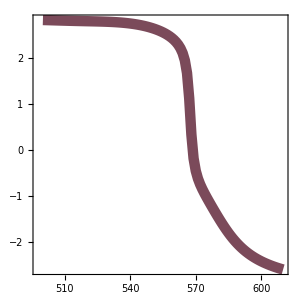

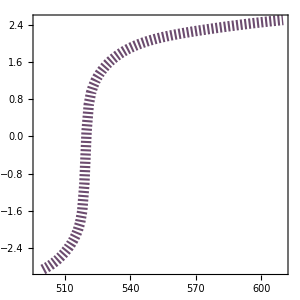

```mathematica
plots = {0,0};
plots[[1]] = ListLinePlot[cuts[[1]],DataRange->lda[[{1,-1}]], Evaluate[graphsOptsPhase],
  PlotStyle->Directive[Thickness[.025]],ColorFunction -> ColorMapSuite["romaO",2]]
plots[[2]] = ListLinePlot[cuts[[2]],DataRange->lda[[{1,-1}]], Evaluate[graphsOptsPhase],
  PlotStyle->Directive[Dashed,Thickness[.025]],ColorFunction -> ColorMapSuite["romaO",2]]
```

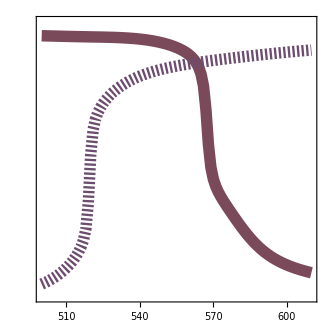

3-TDarkness-Cuts.svg

```mathematica
plot = Show[plots,ImageSize->330, FrameTicks->{{ticks,Automatic},{Automatic,Automatic}},PlotRange->{-π,π}]
Export["3-TDarkness-Cuts.svg",plot]
```

## Prior Sensitivity

```mathematica
aRad = {30.,17.5};
cfrac = 0.12; rho = 0.275/(π*aRad[[2]]^2);
nNP = JohnsonChristyAuRefSize[#1,#2]& ;

ang = {72,70};
lda = Range[500,610,.1];
ldaSPP = Range[600,900,.1];
nMat = 1.33 + Range[.0,.03,.0025]
```

{1.33,1.3325,1.335,1.3375,1.34,1.3425,1.345,1.3475,1.35,1.3525,1.355,1.3575,1.36}

### Data y rama del argumento

```mathematica
data = ConstantArray[0,{2, Length[nMat],Length[lda]}];
Table[
  nMatrix = nMat[[j]];
  indicesCSM = Transpose[Table[{nMatrix,nNP[i,aRad[[1]]],1.5},{i,lda}]];
  epsilon = Transpose[Table[{nMatrix,nNP[i,aRad[[2]]],1.5}^2,{i,lda}]];
  
  data[[1,j]] = CSM3MediaElipsometryInt[ang[[1]]*Pi/180., indicesCSM, lda, aRad[[1]], cfrac][[2]];
  data[[2,j]] = ThinFimlElipsometryInt[ang[[2]]*Pi/180., epsilon, lda, aRad[[2]], rho][[2]];
,{j,Length[nMat]}];
```

```mathematica
data[[1,;;2]] = data[[1,;;2]] /. x_->(Mod[x,2π,-2π]+π);
data[[1,3;;]] = data[[1,3;;]] /. x_->(x+π);
data[[2,;;6]] = data[[2,;;6]] /. x_->(Mod[x,2π+.8,-2π]+π);
data[[2,7;;]] = data[[2,7;;]] /. x_->(Mod[x,2π,-2π]+π);
```

{-Graphics-,-Graphics-}

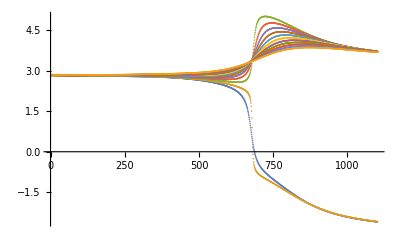
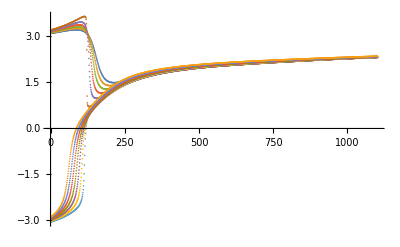

```mathematica
ListDensityPlot[#,PlotRange->Full]&/@ data
ListPlot[#,PlotRange->All]&/@ data
```

### Graficas

```mathematica
dataLda = {0,0};
dataLda[[1]] = Map[Transpose[{lda,#}]&,data,{2}];
dataLda[[2]] = Map[CentralFiniteDifferences[#,1]&,dataLda[[1]],{2}];
dataLda = Transpose[dataLda];
```

```mathematica
lda[[{550,800}]]
```

{554.9,579.9}

```mathematica
plots = {0,0};

plots[[1]] = Map[ListLinePlot[#, Evaluate[graphsOptsS[[1]]],PlotRange->All]&, dataLda[[1,;;,;;,550;;800]]]
plots[[2]] = Map[ListLinePlot[#, Evaluate[graphsOptsS[[1]]],PlotRange->All]&, dataLda[[2,;;,;;,1;;300]]]
```

{RGBColor[0.0036704080323785577, 0.005082388065748999, 0.0024536485544193547],RGBColor[0.04594764835395901, 0.080925694001323, 0.12049430985088669],RGBColor[0.05903600669765248, 0.13830287483816514, 0.21881702718985307],RGBColor[0.07752371216686554, 0.20418675551505294, 0.3274806734242358],RGBColor[0.10778466857783787, 0.2749997036663479, 0.44313719057890116],RGBColor[0.15748896892706943, 0.3482109100138181, 0.5635625836813166],RGBColor[0.2472475422808363, 0.43179156105307254, 0.6850883158005983],RGBColor[0.37050050671094337, 0.5229168964949272, 0.7696881507154507],RGBColor[0.4742132721736469, 0.5913001301421467, 0.7903178160312071],RGBColor[0.5655939191118912, 0.6481618671949725, 0.7896781761873838],RGBColor[0.659056630377618, 0.7078206492697976, 0.792248803968667],RGBColor[0.7636563187961153, 0.7842330779652391, 0.8202144046747256],RGBColor[0.8806634400405308, 0.8857014374760274, 0.8944400971403016],RGBColor[0.9998013720546661, 1., 0.9999611641457039]}

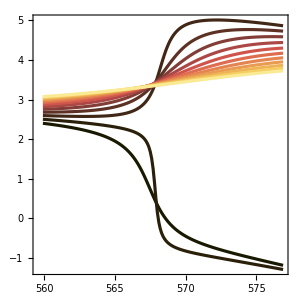
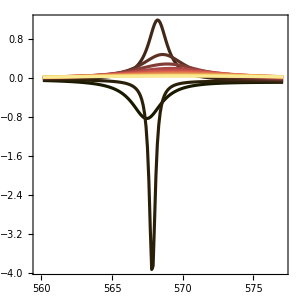

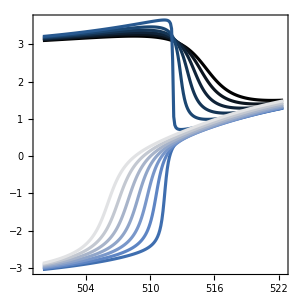
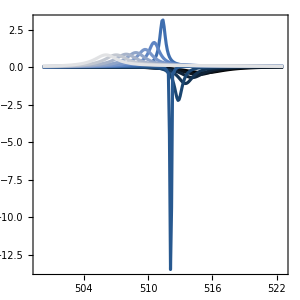

```mathematica
colors2 = ColorMapSuite["oslo"]/@ Range[0,1,1/13.]

plots = {0,0};
plots[[1]] = Map[ListLinePlot[#, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Table[Directive[Thickness[.0075],colors[[i]]],{i,Length[colors]}]]&,
          dataLda[[1,;;,;;,600;;770]]]
plots[[2]] = Map[ListLinePlot[#, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Table[Directive[ Thickness[.0075],colors2[[i]]],{i,Length[colors]}]]&,
          dataLda[[2,;;,;;,1;;225]]]
```

```mathematica
plot = PlotGrid[{#}&/@ Map[Show[#,PlotRange->{{Automatic,Automatic},{All,All}}]&,plots[[;;,1]]] ,Spacings->Scaled[0.125],"ShowFrameLabels"->True,ImageSize->330]
Export["5-Phase.svg",plot]
```

-Graphics-

5-Phase.svg

```mathematica
plots[[1,2]] = Show[#,PlotRange->{{Automatic,Automatic},{-2.5,1.1}}]&@ plots[[1,2]];
plots[[2,2]] = Show[#,PlotRange->{{Automatic,Automatic},{-3,All}}]&@ plots[[2,2]];

plot = PlotGrid[{#}&/@ plots[[;;,2]] ,Spacings->Scaled[0.125],"ShowFrameLabels"->True,ImageSize->330]
Export["5-DerPhase.svg",plot]
```

-Graphics-

5-DerPhase.svg

### Complementary data

#### Metasurface

```mathematica
cdata = ConstantArray[0,{2, 2, Length[nMat],Length[lda]}];

Table[
  nMatrix = nMat[[j]];
  indicesCSM = Transpose[Table[{nMatrix,nNP[i,aRad[[1]]],1.5},{i,lda}]];
  epsilon = Transpose[Table[{nMatrix,nNP[i,aRad[[2]]],1.5}^2,{i,lda}]];
  
  cdata[[1,k,j]] = CSM3MediaElipsometryInt[{70,72}[[k]]*Pi/180., indicesCSM, lda, aRad[[1]], cfrac][[2]];
  cdata[[2,k,j]] = ThinFimlElipsometryInt[{70,72}[[k]]*Pi/180., epsilon, lda, aRad[[2]], rho][[2]];
,{k,2},{j,Length[nMat]}];
```

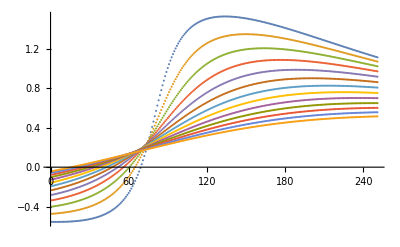
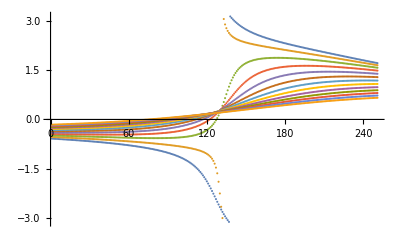
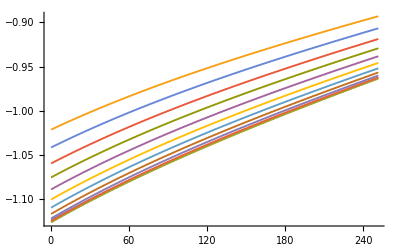
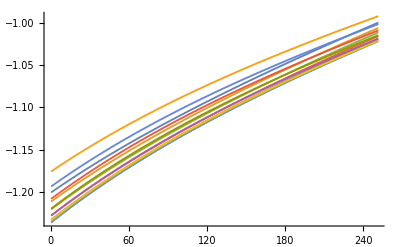

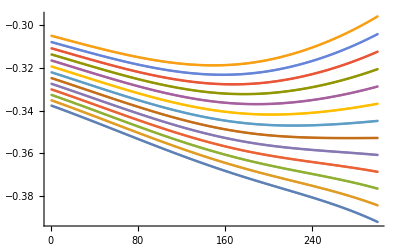
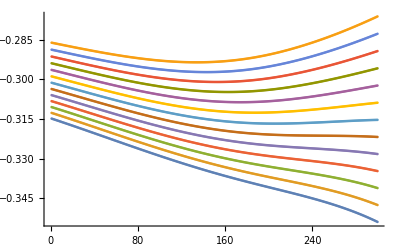
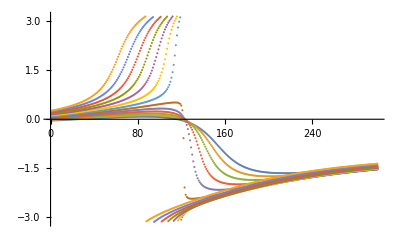
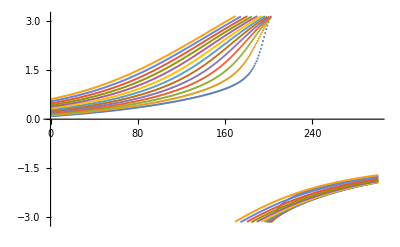

```mathematica
Map[ListPlot,cdata[[;;,;;,;;,550;;800]],{2}]
Map[ListPlot,cdata[[;;,;;,;;,1;;300]],{2}]
```

```mathematica
cdata[[1,2]]=data[[1]];
cdata[[2,1]] = data[[2]];
cdata[[2,2]] = cdata[[2,2]] /.x_ -> Mod[x,2π]-π ;
```

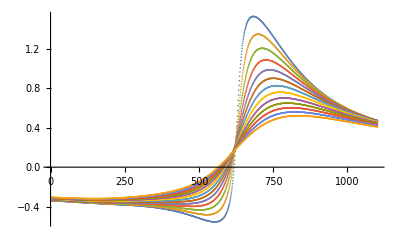
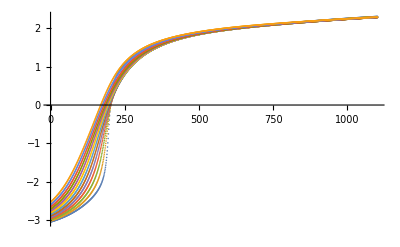
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ListPlot[#,PlotRange->All]&,cdata,{2}]
```

#### SPP

```mathematica
dataSPP = ConstantArray[0,{1, 2, Length[nMat],Length[ldaSPP]}];

Table[
  nMatrix = nMat[[j]];
  indicesSPP = Transpose[Table[{nMatrix,nNP[i,500],1.5},{i,ldaSPP}]];
  dataSPP[[1,k,j]] = norm2@ Landau3MediaReflectionP[{70,72}[[k]]*Pi/180.,Reverse @ indicesSPP,ldaSPP, dfilm]
,{k,2},{j,Length[nMat]}];
```

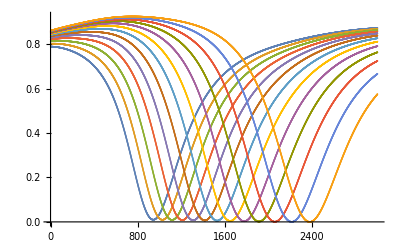
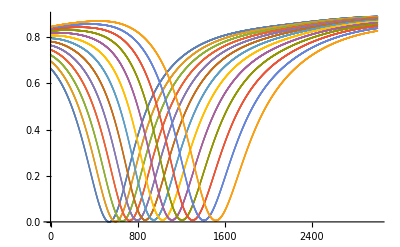

```mathematica
ListPlot /@ dataSPP[[1]]
```

### Sensitivity plots for 70 & 72

#### Data

```mathematica
deltaLambda[list_List]:=(((#1-First[#1]&)[#1⟦All,1⟧]&)[Flatten[#1,1]]&)[(MaximalBy[Abs[#1],Last]&)/@list]
```

```mathematica
dataLda = Map[Transpose[{lda,#}]&,cdata,{3}];
dataLda = Map[CentralFiniteDifferences[#,1]&,dataLda,{3}];

dataLdaSPP = Map[Transpose[{ldaSPP,#}]&,1-dataSPP,{3}];
```

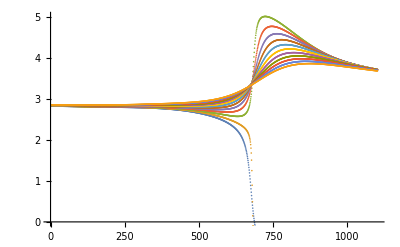
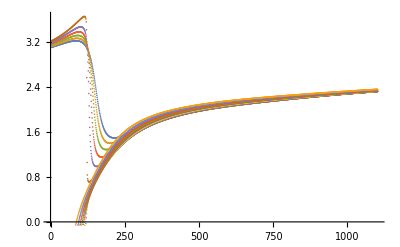
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

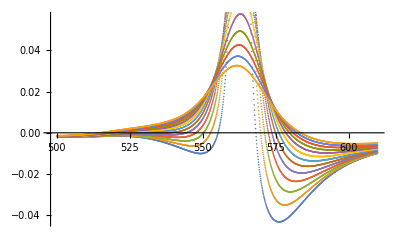
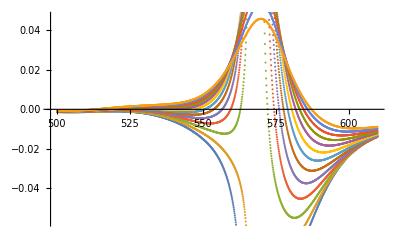
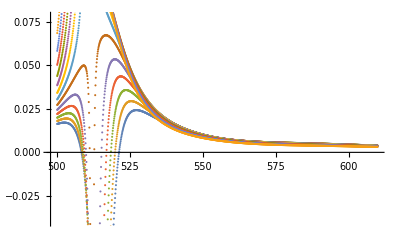
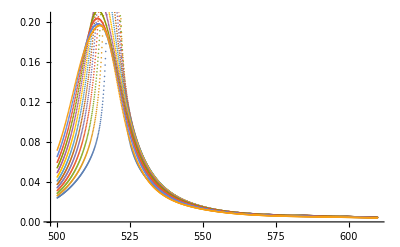

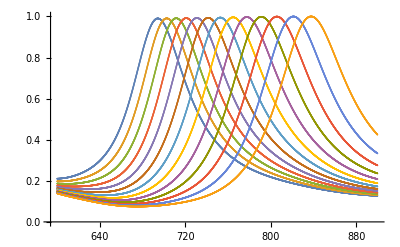
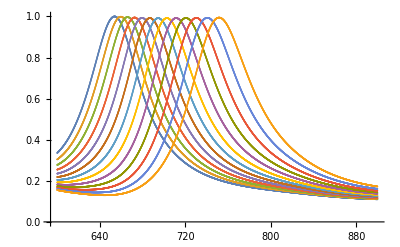

```mathematica
Map[ListPlot,cdata,{2}]
Map[ListPlot,dataLda,{2}]
Map[ListPlot,dataLdaSPP,{2}]
```

#### Plots

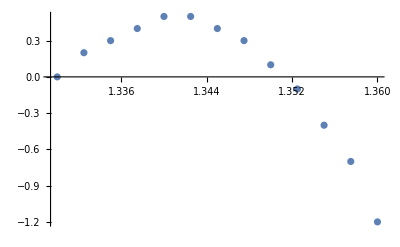
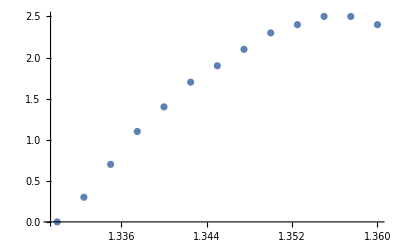
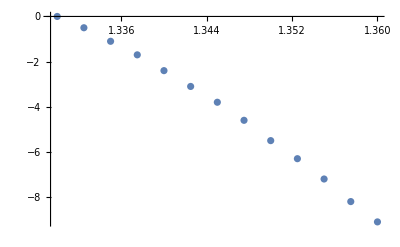
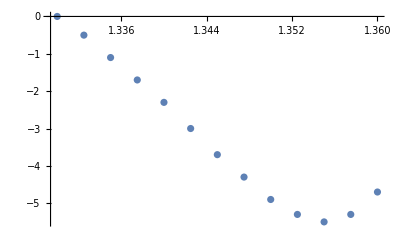

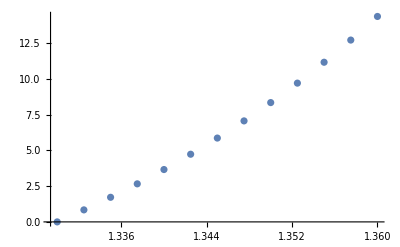
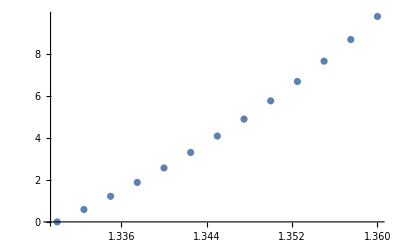

```mathematica
dLda =  Transpose[{nMat,#}]& /@ deltaLambda /@ Flatten[dataLda,1];
ListPlot/@ dLda
dLda = Partition[dLda,2];

dLdaSPP = Transpose[{nMat,#*1*^-1}]& /@ deltaLambda /@ dataLdaSPP[[1]];
ListPlot/@ dLdaSPP
```

```mathematica
plots = {0,0};
 
 plots[[1]] = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03]]]&,
          dLda[[1]]];
plots[[2]] = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03]]]&,
          dLda[[2]]];
AppendTo[plots[[1]], sppPlot = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03],Dashed]]&,
          dLdaSPP]
          ];
AppendTo[plots[[2]],sppPlot];
plots = Partition[Flatten[plots],4];
plot = PlotGrid[{#}&/@ Map[Show[#,PlotRange->{{Automatic,Automatic},{All,10}}]&, plots],Spacings->Scaled[0.125],"ShowFrameLabels"->True,ImageSize->330]
Export["6-SensFrame.svg",plot]
```

-Graphics-

6-SensFrame.svg

```mathematica
plots = {0,0};
 
 plots[[1]] = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03]],
            ColorFunction -> ColorMapSuite[{"lajolla","oslo"}[[First[#2]]],1]]&,
          dLda[[1]]];
plots[[2]] = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03]],
            ColorFunction -> ColorMapSuite[{"lajolla","oslo"}[[First[#2]]],1]]&,
          dLda[[2]]];
AppendTo[plots[[1]], sppPlot = MapIndexed[ListLinePlot[#1,Mesh->All, Evaluate[graphsOptsPhase],PlotRange->All,
            PlotStyle->Directive[Thickness[.01],PointSize[.03],Dashed],
            ColorFunction -> ColorMapSuite[{"lajolla","oslo"}[[First[#2]]],1]]&,
          dLdaSPP]
          ];
AppendTo[plots[[2]],sppPlot];
plots = Partition[Flatten[plots],4];
```

```mathematica
plot = PlotGrid[{#}&/@ Map[Show[#,PlotRange->{{Automatic,Automatic},{All,10}}]&, plots],Spacings->Scaled[0.125],"ShowFrameLabels"->True,ImageSize->330]
Export["6-Sens.svg",plot]
```

-Graphics-

6-Sens.svg